```mathematica
β[ω_,δ_,t_,ϵ_]:=
β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[14],Join[Table[{i,i-1},{i,Range[2,14,1]}],Table[{i,i+1},{i,Range[1,14,1]}],Table[{2n-1,14-2n+2},{n,4}],Table[{14-2n+2,2n-1},{n,3}]]->-t]
```

```mathematica
T1[t_]:=T1[t]=ReplacePart[0*IdentityMatrix[14],Table[{2n,14-2n+1},{n,3}]->t]
```

```mathematica
TT[t_]:=ReplacePart[0*IdentityMatrix[14],Table[{2n,2n},{n,3}]->t]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,0.001,1,0]],B:=Inverse[β[ω,0.001,1,0]],T1:=T1[1]},Do[J=Inverse[IdentityMatrix[14]-B.ConjugateTranspose[T1].J.T1].B,30000]; J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=SR[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=SL[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SL[ω,δ,t,ϵ].TT[t].SR[ω,δ,t,ϵ].TT[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SR[ω,δ,t,ϵ].TT[t].SL[ω,δ,t,ϵ].TT[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].TT[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Abs[Tr[gdd[ω,δ,t,ϵ].TT[t].grr[ω,δ,t,ϵ].TT[t]-TT[t].GNON[ω,δ,t,ϵ].TT[t].GNON[ω,δ,t,ϵ]]]
```

```mathematica
pp=Table[{ω,tr[ω,0.0001,1,0]},{ω,Range[0,4,0.01]}]
```

{{0.,4.34074×10^-6},{0.01,4.35984×10^-6},{0.02,4.41789×10^-6},{0.03,4.51709×10^-6},{0.04,4.66139×10^-6},{0.05,4.85674×10^-6},{0.06,5.11169×10^-6},{0.07,5.43823×10^-6},{0.08,5.85309×10^-6},{0.09,6.37975×10^-6},{0.1,7.05164×10^-6},{0.11,7.9172×10^-6},{0.12,9.0485×10^-6},{0.13,0.0000105561},{0.14,0.0000126159},{0.15,0.000015521},{0.16,0.0000197876},{0.17,0.0000263908},{0.18,0.0000373454},{0.19,0.0000573486},{0.2,0.0000993941},{0.21,0.000210354},{0.22,0.00066514},{0.23,0.00797294},{0.24,0.991909},{0.25,0.999154},{0.26,0.99974},{0.27,0.99989},{0.28,0.999946},{0.29,0.999972},{0.3,0.999986},{0.31,0.999994},{0.32,1.},{0.33,1.},{0.34,1.00001},{0.35,1.00002},{0.36,1.00003},{0.37,1.00004},{0.38,1.00008},{0.39,1.00019},{0.4,1.00066},{0.41,1.00954},{0.42,1.99282},{0.43,1.99912},{0.44,1.9997},{0.45,1.99986},{0.46,1.99992},{0.47,1.99995},{0.48,1.99997},{0.49,1.99998},{0.5,1.99999},{0.51,1.99999},{0.52,1.99999},{0.53,2.},{0.54,2.},{0.55,2.},{0.56,2.},{0.57,2.},{0.58,2.},{0.59,2.},{0.6,2.},{0.61,2.},{0.62,2.},{0.63,2.},{0.64,2.},{0.65,2.},{0.66,2.},{0.67,2.},{0.68,2.},{0.69,2.},{0.7,2.},{0.71,2.},{0.72,2.},{0.73,2.},{0.74,2.},{0.75,2.},{0.76,2.},{0.77,2.00001},{0.78,2.00001},{0.79,2.00002},{0.8,2.00003},{0.81,2.00005},{0.82,2.00011},{0.83,2.00032},{0.84,2.00226},{0.85,2.95484},{0.86,2.99854},{0.87,2.99962},{0.88,2.99984},{0.89,2.99992},{0.9,2.99996},{0.91,2.99997},{0.92,2.99998},{0.93,2.99999},{0.94,2.99999},{0.95,3.},{0.96,3.},{0.97,3.},{0.98,3.},{0.99,3.},{1.,3.},{1.01,3.},{1.02,3.},{1.03,3.},{1.04,3.},{1.05,3.},{1.06,3.},{1.07,3.},{1.08,3.},{1.09,3.},{1.1,3.},{1.11,3.},{1.12,3.},{1.13,3.},{1.14,3.},{1.15,3.},{1.16,3.},{1.17,3.},{1.18,3.},{1.19,3.},{1.2,3.},{1.21,3.},{1.22,3.},{1.23,3.},{1.24,3.},{1.25,3.},{1.26,3.},{1.27,3.},{1.28,3.},{1.29,3.},{1.3,3.},{1.31,3.},{1.32,3.},{1.33,3.},{1.34,3.},{1.35,3.},{1.36,3.},{1.37,3.},{1.38,3.},{1.39,3.},{1.4,3.},{1.41,3.},{1.42,3.},{1.43,3.},{1.44,3.},{1.45,3.},{1.46,3.},{1.47,3.},{1.48,3.},{1.49,3.},{1.5,3.},{1.51,3.},{1.52,3.},{1.53,3.},{1.54,3.},{1.55,3.},{1.56,3.},{1.57,3.},{1.58,3.},{1.59,3.},{1.6,2.99999},{1.61,2.99999},{1.62,2.99999},{1.63,2.99999},{1.64,2.99999},{1.65,2.99999},{1.66,2.99999},{1.67,2.99999},{1.68,2.99999},{1.69,2.99999},{1.7,2.99999},{1.71,2.99999},{1.72,3.},{1.73,3.},{1.74,2.99996},{1.75,2.99966},{1.76,2.99347},{1.77,2.00408},{1.78,2.0002},{1.79,2.00004},{1.8,2.00002},{1.81,2.00001},{1.82,2.},{1.83,2.},{1.84,2.},{1.85,2.},{1.86,2.},{1.87,2.},{1.88,2.},{1.89,2.},{1.9,2.},{1.91,2.},{1.92,2.},{1.93,2.},{1.94,2.},{1.95,2.},{1.96,2.},{1.97,2.},{1.98,2.},{1.99,2.},{2.,2.},{2.01,2.},{2.02,2.},{2.03,2.},{2.04,2.},{2.05,2.},{2.06,2.},{2.07,2.},{2.08,2.},{2.09,2.},{2.1,2.},{2.11,2.},{2.12,2.},{2.13,2.},{2.14,2.},{2.15,2.},{2.16,2.},{2.17,2.},{2.18,2.},{2.19,2.},{2.2,2.},{2.21,1.99999},{2.22,1.99999},{2.23,1.99999},{2.24,1.99999},{2.25,1.99999},{2.26,1.99999},{2.27,1.99999},{2.28,1.99999},{2.29,1.99999},{2.3,1.99999},{2.31,1.99999},{2.32,1.99999},{2.33,1.99999},{2.34,2.},{2.35,2.},{2.36,2.},{2.37,2.},{2.38,1.99998},{2.39,1.9999},{2.4,1.99939},{2.41,1.98782},{2.42,1.00274},{2.43,1.00021},{2.44,1.00005},{2.45,1.00002},{2.46,1.00001},{2.47,1.00001},{2.48,1.},{2.49,1.},{2.5,1.},{2.51,1.},{2.52,1.},{2.53,1.},{2.54,0.999999},{2.55,0.999999},{2.56,0.999999},{2.57,0.999999},{2.58,0.999998},{2.59,0.999998},{2.6,0.999997},{2.61,0.999997},{2.62,0.999997},{2.63,0.999996},{2.64,0.999996},{2.65,0.999995},{2.66,0.999995},{2.67,0.999994},{2.68,0.999994},{2.69,0.999994},{2.7,0.999993},{2.71,0.999993},{2.72,0.999993},{2.73,0.999993},{2.74,0.999994},{2.75,0.999995},{2.76,0.999996},{2.77,0.999997},{2.78,0.999999},{2.79,1.},{2.8,0.999998},{2.81,0.999984},{2.82,0.999928},{2.83,0.999657},{2.84,0.996895},{2.85,0.0243152},{2.86,0.000434578},{2.87,0.0000858531},{2.88,0.0000296068},{2.89,0.000013281},{2.9,6.96612×10^-6},{2.91,4.05834×10^-6},{2.92,2.551×10^-6},{2.93,1.69908×10^-6},{2.94,1.18465×10^-6},{2.95,8.57281×10^-7},{2.96,6.39837×10^-7},{2.97,4.9017×10^-7},{2.98,3.83999×10^-7},{2.99,3.06704×10^-7},{3.,2.49148×10^-7},{3.01,2.05435×10^-7},{3.02,1.71648×10^-7},{3.03,1.45121×10^-7},{3.04,1.24×10^-7},{3.05,1.06969×10^-7},{3.06,9.30768×10^-8},{3.07,8.16254×10^-8},{3.08,7.20952×10^-8},{3.09,6.40935×10^-8},{3.1,5.73205×10^-8},{3.11,5.15444×10^-8},{3.12,4.6584×10^-8},{3.13,4.22967×10^-8},{3.14,3.85687×10^-8},{3.15,3.5309×10^-8},{3.16,3.24437×10^-8},{3.17,2.99128×10^-8},{3.18,2.76669×10^-8},{3.19,2.56654×10^-8},{3.2,2.38745×10^-8},{3.21,2.22659×10^-8},{3.22,2.08157×10^-8},{3.23,1.95041×10^-8},{3.24,1.83139×10^-8},{3.25,1.72306×10^-8},{3.26,1.62418×10^-8},{3.27,1.53368×10^-8},{3.28,1.45063×10^-8},{3.29,1.37425×10^-8},{3.3,1.30382×10^-8},{3.31,1.23874×10^-8},{3.32,1.17847×10^-8},{3.33,1.12256×10^-8},{3.34,1.07058×10^-8},{3.35,1.02217×10^-8},{3.36,9.77014×10^-9},{3.37,9.34814×10^-9},{3.38,8.95317×10^-9},{3.39,8.58293×10^-9},{3.4,8.23537×10^-9},{3.41,7.90865×10^-9},{3.42,7.60112×10^-9},{3.43,7.31126×10^-9},{3.44,7.03774×10^-9},{3.45,6.77933×10^-9},{3.46,6.53491×10^-9},{3.47,6.30348×10^-9},{3.48,6.08411×10^-9},{3.49,5.87597×10^-9},{3.5,5.6783×10^-9},{3.51,5.49039×10^-9},{3.52,5.31159×10^-9},{3.53,5.14133×10^-9},{3.54,4.97904×10^-9},{3.55,4.82425×10^-9},{3.56,4.67648×10^-9},{3.57,4.53531×10^-9},{3.58,4.40034×10^-9},{3.59,4.27122×10^-9},{3.6,4.14761×10^-9},{3.61,4.02918×10^-9},{3.62,3.91566×10^-9},{3.63,3.80677×10^-9},{3.64,3.70226×10^-9},{3.65,3.60189×10^-9},{3.66,3.50545×10^-9},{3.67,3.41274×10^-9},{3.68,3.32355×10^-9},{3.69,3.23771×10^-9},{3.7,3.15506×10^-9},{3.71,3.07544×10^-9},{3.72,2.9987×10^-9},{3.73,2.9247×10^-9},{3.74,2.85331×10^-9},{3.75,2.78441×10^-9},{3.76,2.71788×10^-9},{3.77,2.65362×10^-9},{3.78,2.59152×10^-9},{3.79,2.53149×10^-9},{3.8,2.47344×10^-9},{3.81,2.41728×10^-9},{3.82,2.36292×10^-9},{3.83,2.3103×10^-9},{3.84,2.25934×10^-9},{3.85,2.20996×10^-9},{3.86,2.16211×10^-9},{3.87,2.11572×10^-9},{3.88,2.07074×10^-9},{3.89,2.0271×10^-9},{3.9,1.98476×10^-9},{3.91,1.94366×10^-9},{3.92,1.90376×10^-9},{3.93,1.865×10^-9},{3.94,1.82736×10^-9},{3.95,1.79077×10^-9},{3.96,1.75522×10^-9},{3.97,1.72065×10^-9},{3.98,1.68703×10^-9},{3.99,1.65433×10^-9},{4.,1.62251×10^-9}}

```mathematica
Pri[ω_]:=tr[ω,0.0001,1,0]
```

```mathematica
k14:=k14=Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/14imp100.csv"]
k28:=k28=Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/28imp100.csv"]
k42:=k42=Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/42imp100.csv"]
k56:=k56=Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/56imp100.csv"]
k70:=k70=Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/70imp100.csv"]
k84:=k84=Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/84imp100.csv"]
k100:=k100=Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/100imp100.csv"]
k114:=k114=Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/114imp100.csv"]
k126:=k126=Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/126imp100.csv"]
```

```mathematica
f[ω_]:={Pri[ω],k14[[ω*100+1]][[2]],k28[[ω*100+1]][[2]],k42[[ω*100+1]][[2]],k56[[ω*100+1]][[2]],k70[[ω*100+1]][[2]],k84[[ω*100+1]][[2]],k100[[ω*100+1]][[2]],k114[[ω*100+1]][[2]],k126[[ω*100+1]][[2]]}
```

```mathematica
f[1]
```

{3.,2.39557,1.96898,1.63131,1.39113,1.20677,1.04862,0.917215,0.689114,0.611896}

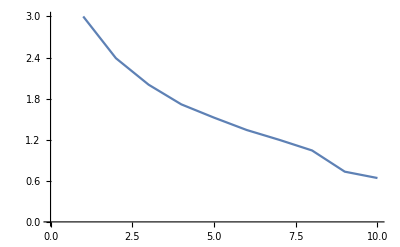

```mathematica
ListLinePlot[f[1.01]]
```

```mathematica
Clear[ββ,ψ]
```

```mathematica
ββ[ω_]:=Table[Table[(*{i,j,*)(f[ω][[j]]-f[ω][[i]])/(j-i)(*}*),{i,2,j-1}],{j,2,4}]
```

```mathematica
ψ[ω_]:=ψ[ω]=-Mean[Flatten[ββ[ω]]]
```

```mathematica
Timing[ψ[1.2]]
```

{0.005784,0.45635}

```mathematica
deltae[ϵ1_,ω_]:=Module[{Tin=T1[1],T=TT[1]},
tra:=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{1,1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{2,2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{3,3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{4,4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{5,5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{6,6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{7,7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{8,8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{9,9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{10,10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{11,11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{12,12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{13,13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={{imp,imp2,imp,imp,imp13,imp,imp,imp10,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp7,imp,imp,imp,imp,imp1,imp,imp,imp,imp,imp4,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp10,imp,imp,imp,imp14,imp11,imp,imp,imp,imp,imp,imp,imp3,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp8,imp,imp,imp,imp,imp,imp,imp4,imp,imp,imp,imp,imp,imp8,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp13,imp}};b=Module[{},
(*Print[Dimensions[list]];*)sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}]; J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
b];tra]
```

```mathematica
deltae[0.5,0]
```

3.14316×10^-7

```mathematica
Table[{ω,ψ[ω]*(tr[ω,0.0001,1,0]-deltae[0.5,ω])},{ω,Range[0.3,1.6,0.01]}]
```

{{0.3,0.0507934},{0.31,0.035307},{0.32,0.00658863},{0.33,0.0421757},{0.34,0.105604},{0.35,0.0432081},{0.36,0.022219},{0.37,0.0363404},{0.38,0.0766421},{0.39,0.0201454},{0.4,0.0596964},{0.41,0.113002},{0.42,0.247601},{0.43,-0.156419},{0.44,-0.0931608},{0.45,0.372001},{0.46,0.345322},{0.47,0.317045},{0.48,0.571195},{0.49,0.313888},{0.5,0.346829},{0.51,0.442022},{0.52,0.431173},{0.53,0.337844},{0.54,0.510146},{0.55,0.260624},{0.56,0.192867},{0.57,0.488892},{0.58,0.313219},{0.59,0.297875},{0.6,0.23577},{0.61,0.23611},{0.62,0.218999},{0.63,0.269514},{0.64,0.175164},{0.65,0.167276},{0.66,0.3398},{0.67,0.40039},{0.68,0.167825},{0.69,0.175085},{0.7,0.187301},{0.71,0.198939},{0.72,0.0626939},{0.73,0.206763},{0.74,0.115852},{0.75,0.143066},{0.76,0.185472},{0.77,0.19185},{0.78,0.140637},{0.79,0.0950533},{0.8,0.211788},{0.81,0.17219},{0.82,0.195739},{0.83,0.246219},{0.84,0.285082},{0.85,0.293009},{0.86,0.0561091},{0.87,-0.182615},{0.88,1.11077},{0.89,1.39939},{0.9,1.41018},{0.91,1.25267},{0.92,1.20508},{0.93,1.14759},{0.94,1.15986},{0.95,0.707703},{0.96,0.67766},{0.97,0.901623},{0.98,0.626548},{0.99,0.809827},{1.,0.771036},{1.01,0.568373},{1.02,0.750074},{1.03,0.814351},{1.04,1.30782},{1.05,0.745081},{1.06,0.108888},{1.07,0.0887431},{1.08,0.458784},{1.09,0.613314},{1.1,0.860871},{1.11,1.21864},{1.12,1.25731},{1.13,1.03696},{1.14,1.3582},{1.15,1.15056},{1.16,1.19209},{1.17,1.37803},{1.18,1.3172},{1.19,1.15701},{1.2,1.33065},{1.21,1.20105},{1.22,1.28757},{1.23,0.957723},{1.24,1.35835},{1.25,1.28035},{1.26,1.01955},{1.27,1.12458},{1.28,1.18726},{1.29,1.09289},{1.3,1.20688},{1.31,1.06537},{1.32,0.781525},{1.33,0.957823},{1.34,0.949105},{1.35,0.900114},{1.36,0.84817},{1.37,0.990673},{1.38,0.899567},{1.39,1.26902},{1.4,1.26115},{1.41,1.27787},{1.42,0.957252},{1.43,1.12164},{1.44,0.84472},{1.45,1.07603},{1.46,1.18791},{1.47,0.817661},{1.48,1.05536},{1.49,0.664182},{1.5,1.16616},{1.51,0.777005},{1.52,0.93908},{1.53,0.975368},{1.54,1.20407},{1.55,1.08838},{1.56,1.14313},{1.57,1.21968},{1.58,1.3253},{1.59,1.04816},{1.6,1.31618}}

```mathematica
Integrate[Interpolation[Table[{ω,ψ[ω]*(tr[ω,0.0001,1,0]-deltae[0.5,ω])},{ω,Range[0.3,1.6,0.01]}]][ω],{ω,0.3,1.6}]/Integrate[Interpolation[Table[{ω,ψ[ω]*ψ[ω]},{ω,Range[0.3,1.6,0.01]}]][ω],{ω,0.3,1.6}]
```

5.35005

```mathematica
misfit[ϵ1_,x_,y_]:=Module[{Tin=T1[1],T=TT[1]},
tra:=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{1,1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{2,2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{3,3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{4,4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{5,5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{6,6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{7,7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{8,8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{9,9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{10,10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{11,11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{12,12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{13,13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp9,imp6,imp,imp13,imp1,imp2,imp,imp5,imp3,imp,imp14,imp,imp11,imp7,imp8,imp4,imp12,imp14,imp11,imp3,imp12,imp13,imp9,imp8,imp13,imp10,imp3,imp5,imp4,imp14,imp,imp9,imp,imp10,imp2,imp7,imp,imp3,imp11,imp13,imp3,imp11,imp6,imp10,imp7,imp2,imp,imp,imp9,imp,imp5,imp13,imp13,imp,imp6,imp13,imp7,imp7,imp3,imp13,imp2,imp2,imp1,imp14,imp6,imp,imp11,imp,imp10,imp5,imp6,imp7,imp8,imp,imp7,imp2,imp10,imp11,imp9,imp3,imp13,imp1,imp,imp13,imp14,imp6,imp4,imp14,imp10,imp1,imp13,imp9,imp7,imp4,imp3,imp,imp10,imp4,imp10,imp3}]};b=Module[{},
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}]; J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
b];
m5=Table[{ω,tra},{ω,Range[0,4,0.01]}];
υ=Module[{},
ρ1:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]-pp[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ2:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/14imp100.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ3:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/28imp100.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ4:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/42imp100.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ5:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/56imp100.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ6:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/70imp100.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ7:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/84imp100.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ8:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/100imp100.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ9:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/114imp100.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ10:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/126imp100.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ11:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/140imp100.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
list:={{1,ρ2},{2,ρ3},{3,ρ4},{4,ρ5},{5,ρ6},{6,ρ7},{7,ρ8},{8,ρ9},{9,ρ10},{10,ρ11},{11,ρ1}};
{ListPlot[list],list[[Position[list,Min[list]][[1,1]],1]],{ρ1,ρ4,ρ8},((16(ρ9-ρ1)-64(ρ5-ρ1))/(4(ρ9-ρ1)-8(ρ5-ρ1)))/2}];
υ]
```

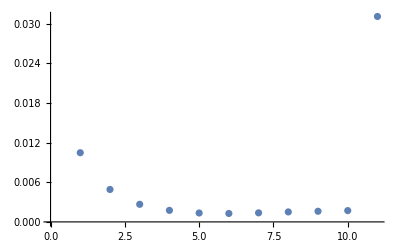
{-Graphics-,6,{0.0310732,0.00266152,0.00136885},6.0322}

```mathematica
misfit[0.5,1.5,0]
```

```mathematica
Table[{misfit[0.5,1.5,0][[4]],misfit[0.5,1.5,0][[2]]},10]
```

{{7.02149,7},{7.05721,7},{7.08369,7},{7.00385,7},{6.96653,7},{7.04026,7},{7.05046,7},{7.04204,7},{7.03918,7},{7.02263,7}}

```mathematica
First/@First[GatherBy[SortBy[%416,Last],Last]]
```

{5.7936,5.7994,5.80255,5.80289,5.80343,5.82456,5.82723,5.82882,5.86064}

```mathematica
First/@Last[GatherBy[SortBy[%416,Last],Last]]
```

{5.78291,5.79404,5.80076,5.80673,5.81993,5.83791,5.84281,5.84318,5.86084}

```mathematica
First/@%416
```

{5.80255,5.85266,5.82882,5.84636,5.84803,5.84832,5.82723,5.81653,5.84318,5.83972,5.85684,5.88262,5.85626,5.84132,5.82456,5.81338,5.81993,5.80289,5.8448,5.7936,5.79404,5.82277,5.86166,5.81255,5.79784,5.78908,5.80322,5.78021,5.84281,5.84368,5.82478,5.82754,5.83965,5.84468,5.82288,5.83229,5.81138,5.85816,5.85418,5.82659,5.83205,5.83069,5.78291,5.84623,5.83345,5.78695,5.83591,5.79109,5.86297,5.8097,5.81232,5.82228,5.82517,5.83509,5.79186,5.82319,5.85794,5.83011,5.82823,5.84884,5.80343,5.81051,5.80185,5.83791,5.7646,5.80076,5.87006,5.87682,5.81398,5.83677,5.80727,5.82495,5.81481,5.77424,5.74503,5.81279,5.84496,5.84979,5.8175,5.83923,5.86084,5.85357,5.80785,5.82933,5.8171,5.86064,5.87999,5.8042,5.82352,5.8423,5.85079,5.7994,5.82228,5.79851,5.82745,5.86093,5.80673,5.83036,5.82341,5.82705}

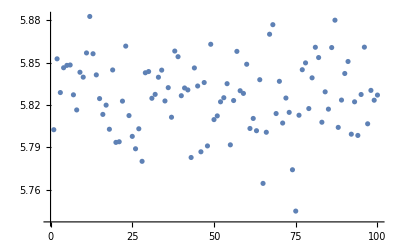

```mathematica
ListPlot[%417]
```

```mathematica
min[n1_,n2_,χ1_,χ2_]:=(n1*n1(misfit[0.5,1.5,0][[2]][[χ2]]-misfit[0.5,1.5,0][[2]][[1]])-n2*n2(misfit[0.5,1.5,0][[2]][[χ1]]-misfit[0.5,1.5,0][[2]][[1]]))/(n1(misfit[0.5,1.5,0][[2]][[χ2]]-misfit[0.5,1.5,0][[2]][[1]])-n2(misfit[0.5,1.5,0][[2]][[χ1]]-misfit[0.5,1.5,0][[2]][[1]]))/2
```

```mathematica
min[3,7,2,3]
```

4.39633

```mathematica
Tally[{imp5,imp,imp,imp12,imp10,imp,imp,imp8,imp,imp13,imp,imp14,imp,imp4,imp10,imp,imp1,imp13,imp,imp9,imp2,imp,imp13,imp,imp6,imp,imp,imp7,imp5,imp,imp,imp,imp1,imp,imp,imp,imp,imp,imp,imp,imp5,imp,imp,imp7,imp,imp9,imp7,imp5,imp8,imp,imp,imp,imp5,imp7,imp,imp,imp,imp,imp,imp4,imp14,imp8,imp,imp11,imp,imp7,imp,imp,imp4,imp8,imp,imp11,imp6,imp4,imp1,imp,imp,imp,imp,imp6,imp,imp11,imp8,imp10,imp,imp14,imp,imp13,imp,imp,imp1,imp5,imp6,imp,imp,imp12,imp14,imp2,imp,imp}]
```

{{imp5,6},{imp,52},{imp12,2},{imp10,3},{imp8,5},{imp13,4},{imp14,4},{imp4,4},{imp1,4},{imp9,2},{imp2,2},{imp6,4},{imp7,5},{imp11,3}}

```mathematica
RandomSample[Join[RandomChoice[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14},84],Table[imp,16]],100]
```

{imp9,imp6,imp,imp13,imp1,imp2,imp,imp5,imp3,imp,imp14,imp,imp11,imp7,imp8,imp4,imp12,imp14,imp11,imp3,imp12,imp13,imp9,imp8,imp13,imp10,imp3,imp5,imp4,imp14,imp,imp9,imp,imp10,imp2,imp7,imp,imp3,imp11,imp13,imp3,imp11,imp6,imp10,imp7,imp2,imp,imp,imp9,imp,imp5,imp13,imp13,imp,imp6,imp13,imp7,imp7,imp3,imp13,imp2,imp2,imp1,imp14,imp6,imp,imp11,imp,imp10,imp5,imp6,imp7,imp8,imp,imp7,imp2,imp10,imp11,imp9,imp3,imp13,imp1,imp,imp13,imp14,imp6,imp4,imp14,imp10,imp1,imp13,imp9,imp7,imp4,imp3,imp,imp10,imp4,imp10,imp3}